```mathematica
rfs = ;
```

```mathematica
nrus = {57, 53.76, 50.16, 50.1, 48.48,45.18, 43.52, 42.22, 39.98};
```

```mathematica
Select[rfs, MemberQ[nrus, #fitness]&]
```

{<|RuleNumber→3737245648,Colors→2,Range→2,fitness→39.98|>,<|RuleNumber→2730967050,Colors→2,Range→2,fitness→39.98|>,<|RuleNumber→2060009122,Colors→2,Range→2,fitness→50.16|>,<|RuleNumber→2862463118,Colors→2,Range→2,fitness→50.1|>,<|RuleNumber→2152543088,Colors→2,Range→2,fitness→45.18|>,<|RuleNumber→3892902626,Colors→2,Range→2,fitness→42.22|>,<|RuleNumber→4036860486,Colors→2,Range→2,fitness→50.16|>,<|RuleNumber→2335014020,Colors→2,Range→2,fitness→53.76|>,<|RuleNumber→3328502170,Colors→2,Range→2,fitness→48.48|>,<|RuleNumber→247268050,Colors→2,Range→2,fitness→43.52|>}

```mathematica
Labeled[ArrayPlot[CellularAutomaton[{#RuleNumber, 2, 2},RandomInteger[1,400],300]], #fitness]&/@Select[rfs, MemberQ[Most[nrus], #fitness]&]
```

{-Graphics-50.16,-Graphics-50.1,-Graphics-45.18,-Graphics-42.22,-Graphics-50.16,-Graphics-53.76,-Graphics-48.48,-Graphics-43.52}

### More colors

```mathematica
rfs31 = Module[{width = 1200, length  = 400},
ParallelMap[With[{tots = Total/@CellularAutomaton[#, RandomInteger[1, width], {{150, 400}}]}, Append[#, "fitness"->N@Abs[Mean[tots[[-50;;]]] - Mean[tots[[;;50]]]]]]&, Table[ResourceFunction["RandomCA"][{3, 1}, "Quiescent"->True], 10000]]];
```

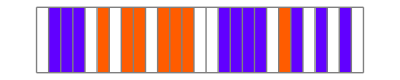

```mathematica
RuleSequencePlot[{ResourceFunction["RandomCA"][{3, 1}, "Quiescent"->True]["RuleNumber"], 3, 1}]
```

```mathematica
ArrayPloCellularAutomaton[{#RuleNumber, 3, 1},RandomInteger[1,400],300]&/@ReverseSortBy[rfs31, #fitness&][[;;1]]
```

```mathematica
ReverseSortBy[rfs31, #fitness&][[;;1]]
```

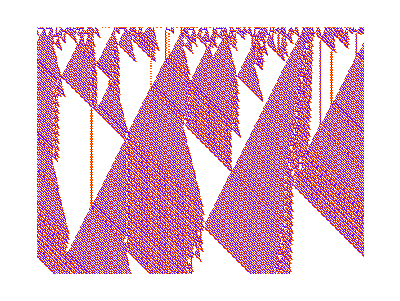
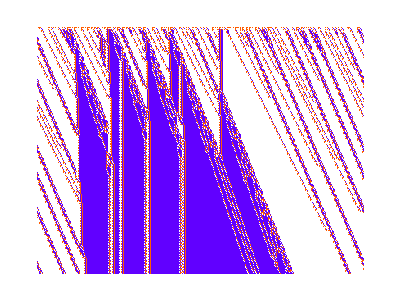
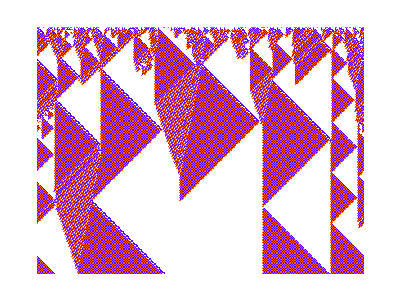
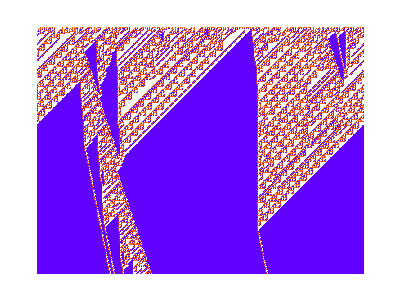
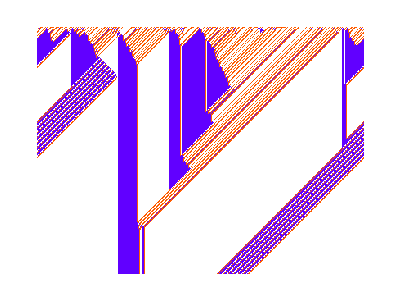
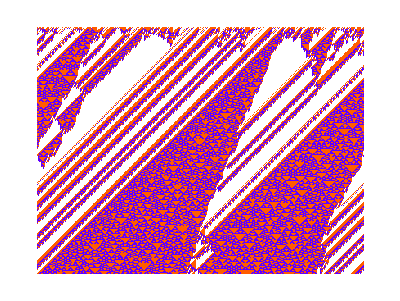
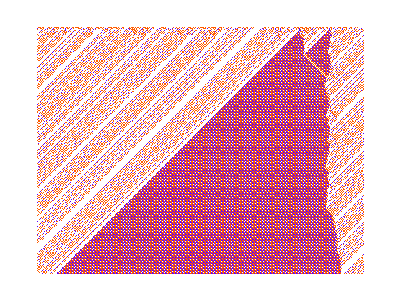
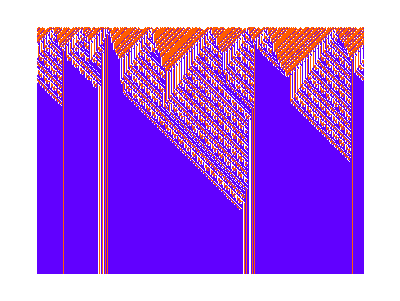
{-Graphics-828.04,-Graphics-638.56,-Graphics-474.58,-Graphics-464.68,-Graphics-453.1,-Graphics-388.02,-Graphics-370.16,-Graphics-368.58,-Graphics-366.9,-Graphics-366.78}

```mathematica
Labeled[ArrayPlot[CellularAutomaton[{#RuleNumber, 3, 1},RandomInteger[1,400],300], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]], #fitness]&/@ ReverseSortBy[rfs31, #fitness&][[;;10]]
```

```mathematica
Labeled[ArrayPlot[CellularAutomaton[{#RuleNumber, 3, 1},RandomInteger[1,400],1000], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]], #fitness]&/@ ReverseSortBy[rfs31, #fitness&][[100;;120]]
```

{-Graphics-120.92,-Graphics-120.14,-Graphics-120.1,-Graphics-119.32,-Graphics-118.88,-Graphics-117.,-Graphics-116.96,-Graphics-115.86,-Graphics-115.58,-Graphics-113.8,-Graphics-113.66,-Graphics-112.72,-Graphics-111.6,-Graphics-110.98,-Graphics-110.56,-Graphics-108.54,-Graphics-107.,-Graphics-104.92,-Graphics-104.8,-Graphics-103.62,-Graphics-101.88}

```mathematica
ParallelMap[Labeled[ArrayPlot[CellularAutomaton[{#RuleNumber, 3, 1},RandomInteger[1,1000],1000], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]], #fitness]&,ReverseSortBy[rfs31, #fitness&][[121;;200]]]
```

{-Graphics-101.66,-Graphics-101.44,-Graphics-101.1,-Graphics-100.46,-Graphics-97.12,-Graphics-97.,-Graphics-96.98,-Graphics-96.72,-Graphics-96.14,-Graphics-96.02,-Graphics-95.88,-Graphics-95.08,-Graphics-94.64,-Graphics-94.3,-Graphics-94.12,-Graphics-93.42,-Graphics-93.16,-Graphics-93.06,-Graphics-92.42,-Graphics-92.14,-Graphics-91.96,-Graphics-91.78,-Graphics-91.68,-Graphics-91.4,-Graphics-91.38,-Graphics-91.1,-Graphics-91.08,-Graphics-91.,-Graphics-90.82,-Graphics-90.82,-Graphics-89.68,-Graphics-88.96,-Graphics-88.52,-Graphics-88.48,-Graphics-88.18,-Graphics-88.18,-Graphics-88.06,-Graphics-87.62,-Graphics-86.98,-Graphics-86.78,-Graphics-86.22,-Graphics-85.1,-Graphics-84.94,-Graphics-83.64,-Graphics-83.3,-Graphics-83.06,-Graphics-82.8,-Graphics-82.68,-Graphics-82.38,-Graphics-81.94,-Graphics-81.82,-Graphics-81.,-Graphics-80.16,-Graphics-80.02,-Graphics-78.9,-Graphics-78.78,-Graphics-78.62,-Graphics-78.12,-Graphics-77.9,-Graphics-77.4,-Graphics-76.98,-Graphics-76.74,-Graphics-76.72,-Graphics-75.66,-Graphics-74.88,-Graphics-74.02,-Graphics-73.96,-Graphics-73.18,-Graphics-72.78,-Graphics-72.28,-Graphics-71.64,-Graphics-71.58,-Graphics-70.78,-Graphics-70.68,-Graphics-70.52,-Graphics-70.5,-Graphics-70.3,-Graphics-70.18,-Graphics-69.98,-Graphics-69.92}

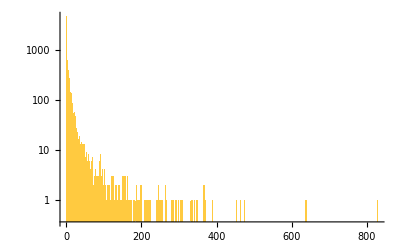

```mathematica
Histogram[#fitness&/@rfs31, PlotRange->All,ScalingFunctions->"Log"]
```